### Notes from 4/15/2021

#### Normalization

When we write our normal modes as

q_n = ∑_(i=1)^(3N) l_i^(n)Δ x_i

We can visualize the OH stretch

```mathematica
vizualizeRPathMode[
q12OHReactionPathData,
q12OHFChkData,
1,
2,
-2., 2., .5
]
```

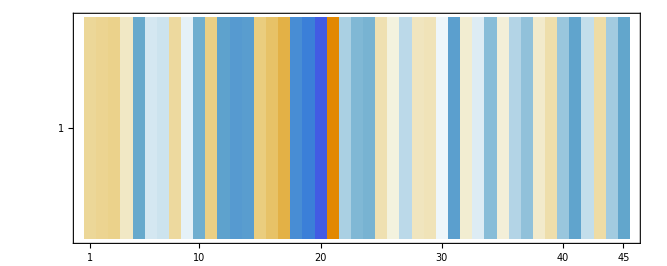

```mathematica
q12OHReactionPathData[[1, "Modes", 39]]//ArrayReshape[#, {1, Length[#]}]&//MatrixPlot
```

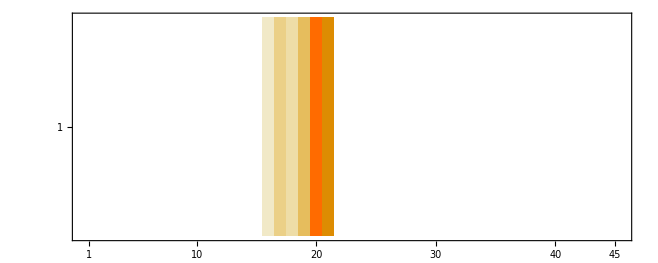

```mathematica
Round[100*q12OHReactionPathData[[1, "Modes", -1]]^2,
.01
]//ArrayReshape[#, {1, Length[#]}]&//MatrixPlot
```

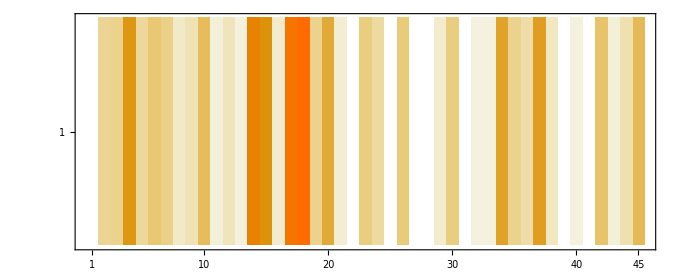

```mathematica
Round[100*q12OHReactionPathData[[1, "Modes", 2]]^2,
.01
]//ArrayReshape[#, {1, Length[#]}]&//MatrixPlot
```

where the colors just represent l_i^(n)

A key point of this is that the normal modes are normalized, i.e.

```mathematica
q12OHReactionPathData[[1, "Modes", 39]]//Norm
```

1.

this is basically calculating a distance by

√(l_1^2+l_2^2+...+(l_(3N))^2)=1

note that this is the same as for wave functions, i.e. we would write

BraKet[{n  }, {  n}] = 1

A second important point is that they are mutually orthogonal!

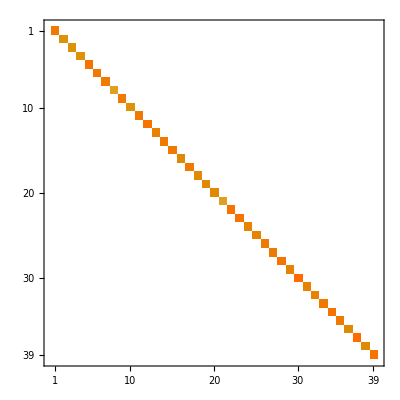

```mathematica
q12OHReactionPathData[[1, "Modes"]].Transpose[q12OHReactionPathData[[1, "Modes"]]]//Threshold//MatrixPlot
```

note that this is the same as for wave functions, i.e. we would write

n  m=δ_nm

which written like a distance is just

√(l_1^(n)l_1^(m)+l_2^(n)l_2^(m)+...+(l_(3N))^(n)(l_(3N))^(m))=δ_nm

##### Point-to-Point Differences

We can also write our normal modes at one point as linear combinations of the modes at a different point! i.e. for points 13 and 15

q_n^(13) = ∑_(i=1)^(3N-6) c_i^(15)q_i^(15)

and these coefficients can be calculated really easily if we have them expressed in the same set of Cartesian displacements by

q_n^(13) = ∑_(i=1)^(3N-6) q_i^(15) q_n^(13)q_i^(15)

where that overlap is just the dot product of the coefficient vectors when expressing the normal modes as linear combinations of Cartesian displacements

q_i^(15) q_n^(13) = l^(15).l^(13)

this is analogous to the way we talk about projection operators in 550, i.e. we can write a wavefunction in terms of an original basis of states

ψ_n=∑_i ϕ_iϕ_i ψ_n
=ψ_n∑_i ϕ_iϕ_i

which is why we write the identity as

I=∑_i ϕ_iϕ_i

What is interesting now is how this applies from point to point

```mathematica
q12OHReactionPathData[[13, "Modes", 10]]
```

{-0.268191,0.0932447,-0.0495078,-0.266407,-0.094704,-0.0912406,0.273493,-0.0467112,0.0804837,0.440462,0.00866607,-0.0200848,0.101403,-0.263715,-0.049338,0.368252,-0.0148593,-0.0116795,0.170511,0.130086,0.211918,-0.317742,0.0899188,0.089339,-0.105531,-0.00425916,0.0175471,-0.125144,0.0289696,0.0487841,-0.0763414,0.0128509,0.00224523,0.0732205,0.154898,0.0120023,0.102289,0.0634521,0.0137237,0.0657723,-0.0850261,0.0317338,0.0719225,0.162022,-0.0072893}

```mathematica
q12OHReactionPathData[[13, "Modes", 12]].q12OHReactionPathData[[13, "Modes", 10]]
```

-3.62356×10^-16

```mathematica
q12OHReactionPathData[[15, "Modes", 12]].q12OHReactionPathData[[13, "Modes", 10]]
```

0.175907

```mathematica
q12OHReactionPathData[[15, "Modes", 12]].q12OHReactionPathData[[13, "Modes", 12]]
```

0.54432

```mathematica
100*(q12OHReactionPathData[[15, "Modes", 2]].q12OHReactionPathData[[13, "Modes", 3]])^2
```

1.2302

```mathematica
q12OHReactionPathData[[12, "Modes", ]]
```

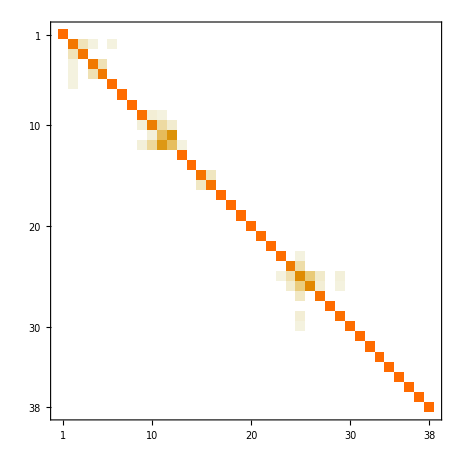

```mathematica
Round[
(q12OHReactionPathData[[15, "Modes"]].Transpose[q12OHReactionPathData[[13, "Modes"]]])^2,
.001
]//Threshold//MatrixPlot
```

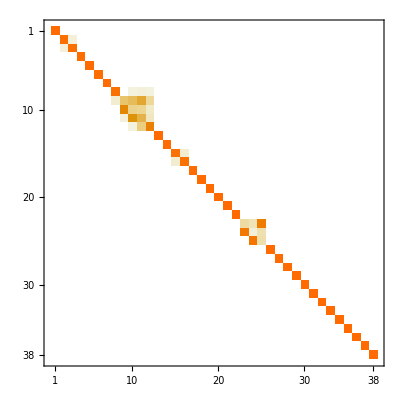
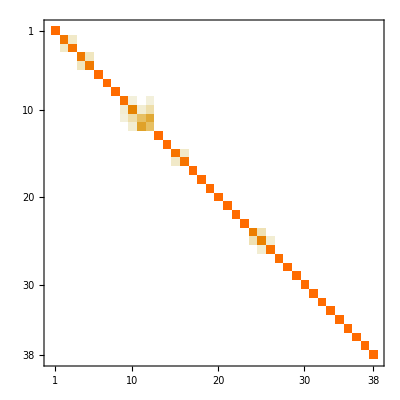
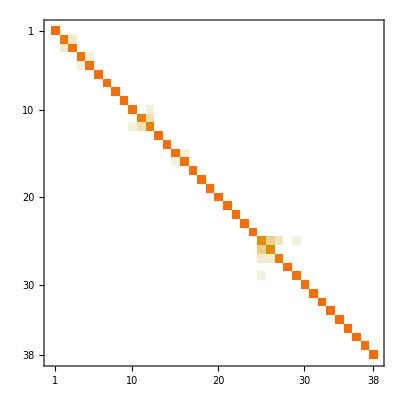
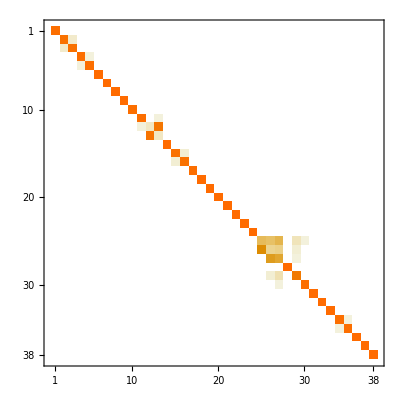
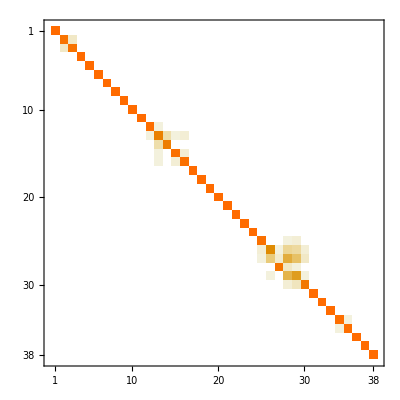
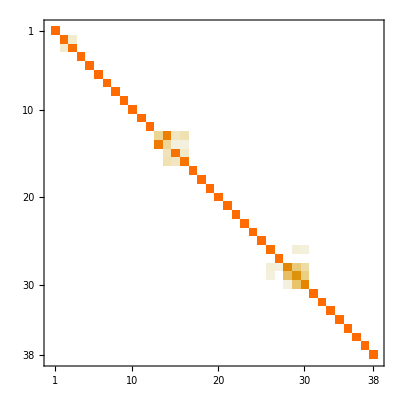
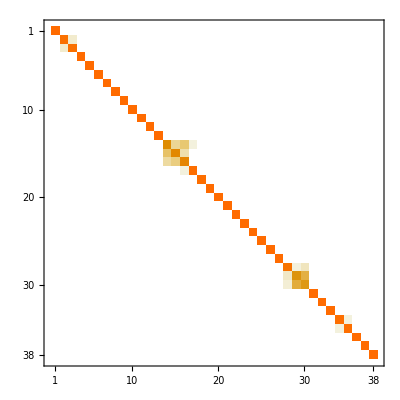
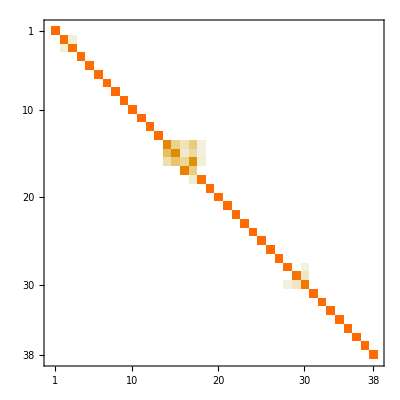

```mathematica
Table[
Round[
(q12OHReactionPathData[[i, "Modes"]].Transpose[q12OHReactionPathData[[i+1, "Modes"]]])^2,
.001
]//Threshold//MatrixPlot,
{i, 12, 20}
]
```

```mathematica
q12OHReactionPathData[[12, "Modes", 13]].q12OHReactionPathData[[22, "Modes", 12]]
```

-0.998462

```mathematica
Round[
(q12OHReactionPathData[[15, "Modes"]].Transpose[q12OHReactionPathData[[16, "Modes"]]])^2,
.001
]//Threshold//MatrixPlot
```

-Graphics-

But if we know what we don’t care about, we can “project it out”, i.e. we can remove the contribution from each of our normal modes that is in the direction of the modes we don’t care about, in 550 world this would look like

P_Interesting=(I-P_Boring)
=I-∑_(b∈Boring) ϕ_bϕ_b

or in our vector world this is

P_Interesting=(I-P_Boring)
=I-∑_(b∈Boring) (l^(b))^Τ l^(b)

what this means in practice is if we can be sure a normal mode doesn’t change much from the shortest OH to longest OH, we define a projection operator onto that mode like

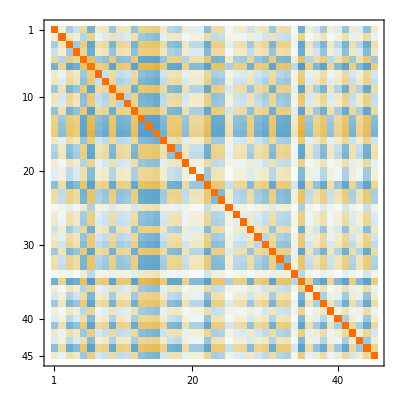

```mathematica
noMoreBreathingMode=IdentityMatrix[Length[q12OHReactionPathData[[12, "Modes", 13]]]]-
Outer[Times, 
q12OHReactionPathData[[12, "Modes", 13]],q12OHReactionPathData[[12, "Modes", 13]]
];
MatrixPlot[noMoreBreathingMode]
```

what this allows us to do is write

P_Interesting L

and this will return only the interesting parts of L! Then we can take overlaps point-wise, but with only the interesting parts of L which should give cleaner trends as we go through

```mathematica
Transpose[
noMoreBreathingMode.
Transpose[q12OHReactionPathData[[15, "Modes"]]]
].(
noMoreBreathingMode.
Transpose[q12OHReactionPathData[[16, "Modes"]]]
)
```

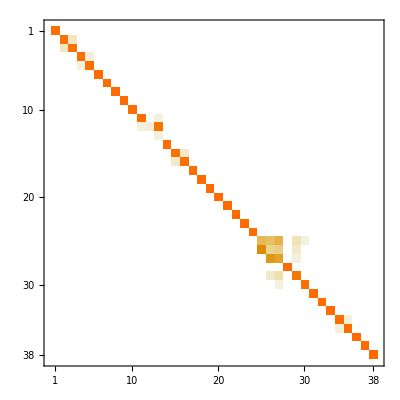

```mathematica
Round[
(
Transpose[
noMoreBreathingMode.
Transpose[q12OHReactionPathData[[15, "Modes"]]]
].(
noMoreBreathingMode.
Transpose[q12OHReactionPathData[[16, "Modes"]]]
)
)^2,
.001
]//Threshold//MatrixPlot
```